```mathematica
(* Computational Methods Lab 5*) 

(*Data of Falling Object*)

densityOfAir = 1.2754; 
dragCoefficient = 0.3;
crossSectionalArea = Pi*0.035^2;
allConstants = 0.5*crossSectionalArea*densityOfAir*dragCoefficient;


(*Initial Conditions*)
vx0 = 150 *Cos[45 Degree]; 
vy0 = 150 * Sin[45 Degree]; 
x0 = 0;
y0 = 1;
deltaT = .1;
v0=((vx0)^2 + (vy0)^2)^0.5;

(*Starting values*)
v = v0; 
vy = vy0;
vx = vx0;
x = x0;
y=y0;
t0 = 0; 

(*list of points*)
pointData = {{t0,x,y,vx0,vy0,v0}}; 
allData= List[{t0,x,y,vx0,vy0,v0}];

(*limits of iterations*)
tmin = 0; 
tmax =  18; 

(*setup iterations*) 

Do [ vyPlus = vy - (9.81+ allConstants*vy^2)*deltaT;
	vy = vyPlus;
	yPlus = y+vy*deltaT + 0.5*9.81*(deltaT)^2;
	y = yPlus;
	xPlus = x+ vx*deltaT; 
	x = xPlus;
	v =((vx)^2 + (vy)^2)^0.5;
			 (*pointData = Append [ pointData, {t,x,y,vx,vy,v}];*)
			allData = AppendTo[allData, {t,x,y,vx,vy,v}],
{t,tmin,tmax,deltaT}
];
(*pointData
xyPoints = Rest[pointData];*)
allData
data1 =Drop[allData, None,{1,1}]; (*remove time*)
data2 = Drop[data1,None,{3,3}]; (*remove vx*)
data3 = Drop[data2,None,{3,3}]; (*remove vy*)
xyData = Drop[data3,None,{3,3}] (*remove v*)
(*xyPoints*)

p1=ListPlot[xyData,PlotRange->{{t0,tmax},{0,0,y}},Joined->True,Frame->True,FrameLabel->{"x(m)","y(m)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
```

{{0,0,1,75 √2,75 √2,150.},{0.,10.6066,11.4747,75 √2,104.257,148.726},{0.1,21.2132,21.7713,75 √2,102.475,147.483},{0.2,31.8198,31.8925,75 √2,100.721,146.27},{0.3,42.4264,41.8409,75 √2,98.9934,145.085},{0.4,53.033,51.619,75 √2,97.2909,143.929},{0.5,63.6396,61.2294,75 √2,95.613,142.8},{0.6,74.2462,70.6743,75 √2,93.959,141.698},{0.7,84.8528,79.9562,75 √2,92.328,140.622},{0.8,95.4594,89.0772,75 √2,90.7194,139.571},{0.9,106.066,98.0395,75 √2,89.1324,138.545},{1.,116.673,106.845,75 √2,87.5665,137.542},{1.1,127.279,115.496,75 √2,86.021,136.564},{1.2,137.886,123.995,75 √2,84.4952,135.608},{1.3,148.492,132.343,75 √2,82.9885,134.674},{1.4,159.099,140.542,75 √2,81.5005,133.762},{1.5,169.706,148.594,75 √2,80.0304,132.872},{1.6,180.312,156.501,75 √2,78.5779,132.002},{1.7,190.919,164.264,75 √2,77.1423,131.152},{1.8,201.525,171.885,75 √2,75.7232,130.323},{1.9,212.132,179.367,75 √2,74.32,129.512},{2.,222.739,186.709,75 √2,72.9323,128.721},{2.1,233.345,193.914,75 √2,71.5597,127.948},{2.2,243.952,200.983,75 √2,70.2017,127.194},{2.3,254.558,207.918,75 √2,68.8578,126.457},{2.4,265.165,214.72,75 √2,67.5278,125.738},{2.5,275.772,221.39,75 √2,66.211,125.036},{2.6,286.378,227.93,75 √2,64.9073,124.35},{2.7,296.985,234.34,75 √2,63.6161,123.681},{2.8,307.591,240.623,75 √2,62.3371,123.028},{2.9,318.198,246.779,75 √2,61.07,122.391},{3.,328.805,252.81,75 √2,59.8144,121.769},{3.1,339.411,258.716,75 √2,58.57,121.163},{3.2,350.018,264.498,75 √2,57.3365,120.571},{3.3,360.624,270.159,75 √2,56.1134,119.995},{3.4,371.231,275.698,75 √2,54.9006,119.432},{3.5,381.838,281.117,75 √2,53.6977,118.884},{3.6,392.444,286.416,75 √2,52.5044,118.35},{3.7,403.051,291.597,75 √2,51.3204,117.829},{3.8,413.657,296.661,75 √2,50.1455,117.323},{3.9,424.264,301.608,75 √2,48.9794,116.829},{4.,434.871,306.439,75 √2,47.8218,116.348},{4.1,445.477,311.155,75 √2,46.6724,115.881},{4.2,456.084,315.758,75 √2,45.531,115.426},{4.3,466.69,320.246,75 √2,44.3974,114.983},{4.4,477.297,324.622,75 √2,43.2713,114.553},{4.5,487.904,328.887,75 √2,42.1524,114.135},{4.6,498.51,333.04,75 √2,41.0406,113.729},{4.7,509.117,337.082,75 √2,39.9356,113.335},{4.8,519.723,341.015,75 √2,38.8372,112.953},{4.9,530.33,344.839,75 √2,37.7451,112.582},{5.,540.937,348.554,75 √2,36.6592,112.223},{5.1,551.543,352.161,75 √2,35.5793,111.874},{5.2,562.15,355.66,75 √2,34.5051,111.537},{5.3,572.756,359.053,75 √2,33.4364,111.211},{5.4,583.363,362.339,75 √2,32.3731,110.896},{5.5,593.97,365.52,75 √2,31.3149,110.592},{5.6,604.576,368.595,75 √2,30.2617,110.299},{5.7,615.183,371.566,75 √2,29.2133,110.016},{5.8,625.79,374.432,75 √2,28.1695,109.743},{5.9,636.396,377.194,75 √2,27.1301,109.481},{6.,647.003,379.852,75 √2,26.0949,109.229},{6.1,657.609,382.408,75 √2,25.0637,108.987},{6.2,668.216,384.86,75 √2,24.0365,108.755},{6.3,678.823,387.211,75 √2,23.013,108.534},{6.4,689.429,389.459,75 √2,21.993,108.322},{6.5,700.036,391.606,75 √2,20.9764,108.12},{6.6,710.642,393.651,75 √2,19.963,107.928},{6.7,721.249,395.595,75 √2,18.9526,107.746},{6.8,731.856,397.439,75 √2,17.9452,107.573},{6.9,742.462,399.182,75 √2,16.9405,107.41},{7.,753.069,400.825,75 √2,15.9383,107.257},{7.1,763.675,402.368,75 √2,14.9386,107.113},{7.2,774.282,403.811,75 √2,13.9412,106.978},{7.3,784.889,405.155,75 √2,12.9459,106.853},{7.4,795.495,406.399,75 √2,11.9525,106.737},{7.5,806.102,407.544,75 √2,10.961,106.631},{7.6,816.708,408.59,75 √2,9.97119,106.534},{7.7,827.315,409.538,75 √2,8.98287,106.446},{7.8,837.922,410.386,75 √2,7.99593,106.367},{7.9,848.528,411.136,75 √2,7.01022,106.297},{8.,859.135,411.788,75 √2,6.0256,106.237},{8.1,869.741,412.341,75 √2,5.04193,106.186},{8.2,880.348,412.796,75 √2,4.05905,106.144},{8.3,890.955,413.153,75 √2,3.07684,106.111},{8.4,901.561,413.411,75 √2,2.09514,106.087},{8.5,912.168,413.572,75 √2,1.11382,106.072},{8.6,922.774,413.634,75 √2,0.13273,106.066},{8.7,933.381,413.598,75 √2,-0.848271,106.069},{8.8,943.988,413.464,75 √2,-1.82932,106.082},{8.9,954.594,413.232,75 √2,-2.81057,106.103},{9.,965.201,412.902,75 √2,-3.79215,106.134},{9.1,975.807,412.474,75 √2,-4.77421,106.173},{9.2,986.414,411.947,75 √2,-5.75689,106.222},{9.3,997.021,411.322,75 √2,-6.74033,106.28},{9.4,1007.63,410.599,75 √2,-7.72467,106.347},{9.5,1018.23,409.777,75 √2,-8.71007,106.423},{9.6,1028.84,408.856,75 √2,-9.69665,106.508},{9.7,1039.45,407.837,75 √2,-10.6846,106.603},{9.8,1050.05,406.719,75 √2,-11.674,106.707},{9.9,1060.66,405.501,75 √2,-12.665,106.819},{10.,1071.27,404.184,75 √2,-13.6578,106.942},{10.1,1081.87,402.768,75 √2,-14.6526,107.073},{10.2,1092.48,401.252,75 √2,-15.6494,107.214},{10.3,1103.09,399.636,75 √2,-16.6484,107.365},{10.4,1113.69,397.921,75 √2,-17.6498,107.524},{10.5,1124.3,396.104,75 √2,-18.6537,107.694},{10.6,1134.91,394.187,75 √2,-19.6604,107.873},{10.7,1145.51,392.169,75 √2,-20.6698,108.061},{10.8,1156.12,390.05,75 √2,-21.6823,108.26},{10.9,1166.73,387.829,75 √2,-22.6979,108.467},{11.,1177.33,385.507,75 √2,-23.7168,108.685},{11.1,1187.94,383.082,75 √2,-24.7392,108.913},{11.2,1198.55,380.554,75 √2,-25.7653,109.151},{11.3,1209.15,377.924,75 √2,-26.7952,109.398},{11.4,1219.76,375.19,75 √2,-27.829,109.656},{11.5,1230.37,372.352,75 √2,-28.867,109.924},{11.6,1240.97,369.411,75 √2,-29.9094,110.202},{11.7,1251.58,366.364,75 √2,-30.9563,110.491},{11.8,1262.19,363.212,75 √2,-32.0078,110.79},{11.9,1272.79,359.955,75 √2,-33.0642,111.1},{12.,1283.4,356.591,75 √2,-34.1257,111.421},{12.1,1294.01,353.121,75 √2,-35.1925,111.752},{12.2,1304.61,349.544,75 √2,-36.2647,112.094},{12.3,1315.22,345.858,75 √2,-37.3425,112.448},{12.4,1325.83,342.065,75 √2,-38.4261,112.812},{12.5,1336.43,338.162,75 √2,-39.5159,113.188},{12.6,1347.04,334.15,75 √2,-40.6118,113.575},{12.7,1357.65,330.028,75 √2,-41.7143,113.974},{12.8,1368.25,325.795,75 √2,-42.8234,114.385},{12.9,1378.86,321.45,75 √2,-43.9394,114.807},{13.,1389.46,316.993,75 √2,-45.0625,115.242},{13.1,1400.07,312.422,75 √2,-46.193,115.688},{13.2,1410.68,307.738,75 √2,-47.3311,116.147},{13.3,1421.28,302.94,75 √2,-48.4771,116.619},{13.4,1431.89,298.025,75 √2,-49.6311,117.104},{13.5,1442.5,292.995,75 √2,-50.7934,117.601},{13.6,1453.1,287.848,75 √2,-51.9644,118.111},{13.7,1463.71,282.582,75 √2,-53.1442,118.635},{13.8,1474.32,277.198,75 √2,-54.3331,119.173},{13.9,1484.92,271.694,75 √2,-55.5315,119.724},{14.,1495.53,266.069,75 √2,-56.7395,120.289},{14.1,1506.14,260.322,75 √2,-57.9576,120.868},{14.2,1516.74,254.453,75 √2,-59.1859,121.462},{14.3,1527.35,248.459,75 √2,-60.4248,122.07},{14.4,1537.96,242.341,75 √2,-61.6746,122.694},{14.5,1548.56,236.097,75 √2,-62.9356,123.332},{14.6,1559.17,229.725,75 √2,-64.2083,123.987},{14.7,1569.78,223.225,75 √2,-65.4928,124.657},{14.8,1580.38,216.595,75 √2,-66.7896,125.343},{14.9,1590.99,209.834,75 √2,-68.099,126.046},{15.,1601.6,202.941,75 √2,-69.4214,126.765},{15.1,1612.2,195.914,75 √2,-70.7573,127.501},{15.2,1622.81,188.752,75 √2,-72.1069,128.255},{15.3,1633.42,181.454,75 √2,-73.4707,129.027},{15.4,1644.02,174.019,75 √2,-74.8491,129.817},{15.5,1654.63,166.443,75 √2,-76.2426,130.625},{15.6,1665.24,158.727,75 √2,-77.6516,131.453},{15.7,1675.84,150.869,75 √2,-79.0765,132.299},{15.8,1686.45,142.866,75 √2,-80.5179,133.166},{15.9,1697.06,134.717,75 √2,-81.9762,134.053},{16.,1707.66,126.421,75 √2,-83.452,134.96},{16.1,1718.27,117.976,75 √2,-84.9457,135.889},{16.2,1728.88,109.379,75 √2,-86.458,136.839},{16.3,1739.48,100.629,75 √2,-87.9893,137.812},{16.4,1750.09,91.724,75 √2,-89.5403,138.807},{16.5,1760.7,82.6619,75 √2,-91.1116,139.826},{16.6,1771.3,73.4406,75 √2,-92.7038,140.869},{16.7,1781.91,64.0579,75 √2,-94.3175,141.936},{16.8,1792.52,54.5116,75 √2,-95.9535,143.028},{16.9,1803.12,44.7994,75 √2,-97.6123,144.146},{17.,1813.73,34.919,75 √2,-99.2948,145.291},{17.1,1824.34,24.8678,75 √2,-101.002,146.463},{17.2,1834.94,14.6435,75 √2,-102.734,147.663},{17.3,1845.55,4.24337,75 √2,-104.492,148.891},{17.4,1856.16,-6.33525,75 √2,-106.277,150.149},{17.5,1866.76,-17.0951,75 √2,-108.089,151.437},{17.6,1877.37,-28.0391,75 √2,-109.93,152.757},{17.7,1887.98,-39.1702,75 √2,-111.801,154.109},{17.8,1898.58,-50.4914,75 √2,-113.702,155.494},{17.9,1909.19,-62.0059,75 √2,-115.635,156.912},{18.,1919.79,-73.7169,75 √2,-117.601,158.367}}

{{0,1},{10.6066,11.4747},{21.2132,21.7713},{31.8198,31.8925},{42.4264,41.8409},{53.033,51.619},{63.6396,61.2294},{74.2462,70.6743},{84.8528,79.9562},{95.4594,89.0772},{106.066,98.0395},{116.673,106.845},{127.279,115.496},{137.886,123.995},{148.492,132.343},{159.099,140.542},{169.706,148.594},{180.312,156.501},{190.919,164.264},{201.525,171.885},{212.132,179.367},{222.739,186.709},{233.345,193.914},{243.952,200.983},{254.558,207.918},{265.165,214.72},{275.772,221.39},{286.378,227.93},{296.985,234.34},{307.591,240.623},{318.198,246.779},{328.805,252.81},{339.411,258.716},{350.018,264.498},{360.624,270.159},{371.231,275.698},{381.838,281.117},{392.444,286.416},{403.051,291.597},{413.657,296.661},{424.264,301.608},{434.871,306.439},{445.477,311.155},{456.084,315.758},{466.69,320.246},{477.297,324.622},{487.904,328.887},{498.51,333.04},{509.117,337.082},{519.723,341.015},{530.33,344.839},{540.937,348.554},{551.543,352.161},{562.15,355.66},{572.756,359.053},{583.363,362.339},{593.97,365.52},{604.576,368.595},{615.183,371.566},{625.79,374.432},{636.396,377.194},{647.003,379.852},{657.609,382.408},{668.216,384.86},{678.823,387.211},{689.429,389.459},{700.036,391.606},{710.642,393.651},{721.249,395.595},{731.856,397.439},{742.462,399.182},{753.069,400.825},{763.675,402.368},{774.282,403.811},{784.889,405.155},{795.495,406.399},{806.102,407.544},{816.708,408.59},{827.315,409.538},{837.922,410.386},{848.528,411.136},{859.135,411.788},{869.741,412.341},{880.348,412.796},{890.955,413.153},{901.561,413.411},{912.168,413.572},{922.774,413.634},{933.381,413.598},{943.988,413.464},{954.594,413.232},{965.201,412.902},{975.807,412.474},{986.414,411.947},{997.021,411.322},{1007.63,410.599},{1018.23,409.777},{1028.84,408.856},{1039.45,407.837},{1050.05,406.719},{1060.66,405.501},{1071.27,404.184},{1081.87,402.768},{1092.48,401.252},{1103.09,399.636},{1113.69,397.921},{1124.3,396.104},{1134.91,394.187},{1145.51,392.169},{1156.12,390.05},{1166.73,387.829},{1177.33,385.507},{1187.94,383.082},{1198.55,380.554},{1209.15,377.924},{1219.76,375.19},{1230.37,372.352},{1240.97,369.411},{1251.58,366.364},{1262.19,363.212},{1272.79,359.955},{1283.4,356.591},{1294.01,353.121},{1304.61,349.544},{1315.22,345.858},{1325.83,342.065},{1336.43,338.162},{1347.04,334.15},{1357.65,330.028},{1368.25,325.795},{1378.86,321.45},{1389.46,316.993},{1400.07,312.422},{1410.68,307.738},{1421.28,302.94},{1431.89,298.025},{1442.5,292.995},{1453.1,287.848},{1463.71,282.582},{1474.32,277.198},{1484.92,271.694},{1495.53,266.069},{1506.14,260.322},{1516.74,254.453},{1527.35,248.459},{1537.96,242.341},{1548.56,236.097},{1559.17,229.725},{1569.78,223.225},{1580.38,216.595},{1590.99,209.834},{1601.6,202.941},{1612.2,195.914},{1622.81,188.752},{1633.42,181.454},{1644.02,174.019},{1654.63,166.443},{1665.24,158.727},{1675.84,150.869},{1686.45,142.866},{1697.06,134.717},{1707.66,126.421},{1718.27,117.976},{1728.88,109.379},{1739.48,100.629},{1750.09,91.724},{1760.7,82.6619},{1771.3,73.4406},{1781.91,64.0579},{1792.52,54.5116},{1803.12,44.7994},{1813.73,34.919},{1824.34,24.8678},{1834.94,14.6435},{1845.55,4.24337},{1856.16,-6.33525},{1866.76,-17.0951},{1877.37,-28.0391},{1887.98,-39.1702},{1898.58,-50.4914},{1909.19,-62.0059},{1919.79,-73.7169}}

ListPlot::prng: Value of option PlotRange -> {{0, 18}, {0, 0, -73.7169}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

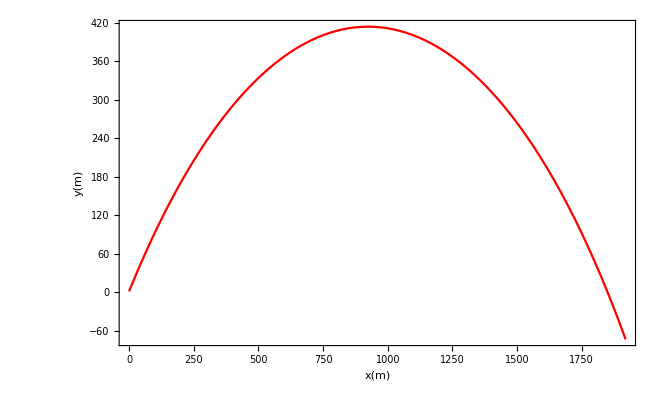
```mathematica
-Graphics-(* Angle = 45 Degree *)
```

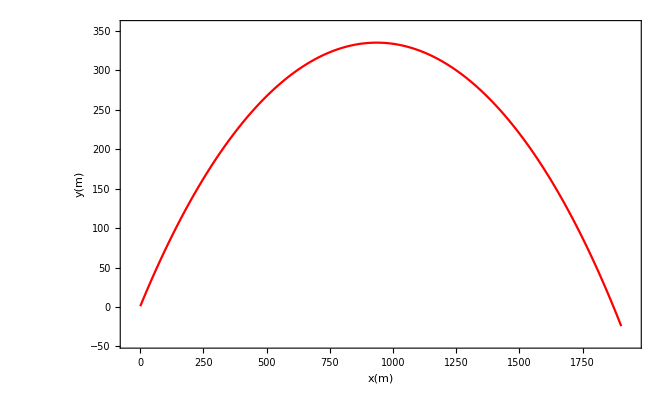
```mathematica
-Graphics-(* Angle = 38 Degree *)
```

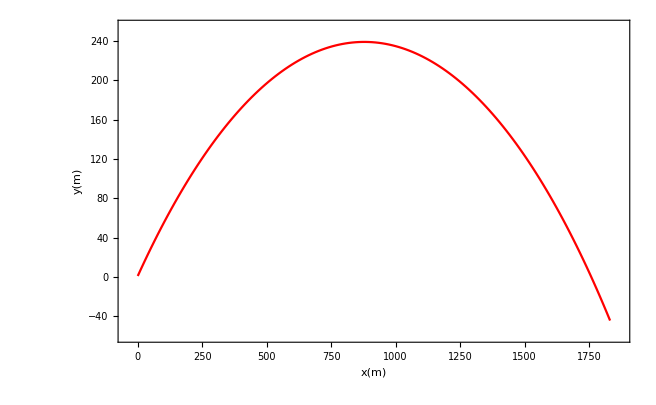
```mathematica
-Graphics-(* Angle = 30 Degree *)
```